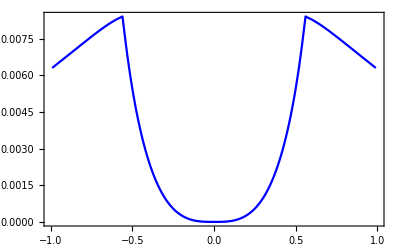

```mathematica
Z1=0;
Z2=0;
Z3=1.58114;
Z4=1.58114;
kFL=1.5Pi;
k=1;
T=0.001;
△=1;
EF=100*△;
β=1/(k*T);
ϕ=0;
SetSharedVariable[list1]
list1={};
ParallelDo[{
ω[N1_]:=(2N1+1)*π/β;
y[N1_]:=(1+p+I*ω[N1]/(EF))^(1/2);
y1[N1_]:=(1-p+I*ω[N1]/(EF))^(1/2);
y3[N1_]:=(1+p-I*ω[N1]/(EF))^(1/2);
y4[N1_]:=(1-p-I*ω[N1]/(EF))^(1/2);
yyy[N1_]:=(1+p+I*ω[N1]/(EF))^(1/2);
yyy1[N1_]:=(1-p+I*ω[N1]/(EF))^(1/2);
yyy3[N1_]:=(1+p-I*ω[N1]/(EF))^(1/2);
yyy4[N1_]:=(1-p-I*ω[N1]/(EF))^(1/2);
yy[N1_]:=(1+p+I*ω[N1]/(EF))^(1/2);
yy1[N1_]:=(1-p+I*ω[N1]/(EF))^(1/2);
yy3[N1_]:=(1+p-I*ω[N1]/(EF))^(1/2);
yy4[N1_]:=(1-p-I*ω[N1]/(EF))^(1/2);
kES[N1_]:=(1+((-ω[N1]^2-△^2)^(1/2))/EF)^(1/2);  
kHS[N1_]:=(1-((-ω[N1]^2-△^2)^(1/2))/EF)^(1/2);
u[N1_]:=(1/2*(1+((-ω[N1]^2-△^2)^(1/2))/(I*ω[N1])))^(1/2);
v[N1_]:= (1/2*(1-((-ω[N1]^2-△^2)^(1/2))/(I*ω[N1])))^(1/2);
G[N1_,ϕ_]:=({{u[N1], 0, 0, v[N1], -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y[N1])/2), 1/2^(1/2), 1/2^(1/2)*E^((I kFL*y1[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -u[N1], -v[N1], 0, -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y[N1])/2), -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y1[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, v[N1], u[N1], 0, 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y3[N1])/2), 1/2^(1/2), 1/2^(1/2)*E^(-(I kFL*y4[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {v[N1], 0, 0, u[N1], 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y3[N1])/2), -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y4[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {u[N1]*kES[N1], 0, 0, -v[N1]*kHS[N1], (y[N1]+2*I*Z1)/2^(1/2), -(y[N1]-2*I*Z1)/2^(1/2)*E^((I kFL*y[N1])/2), -(y1[N1]+2*I*Z1)/2^(1/2), (y1[N1]-2*I*Z1)/2^(1/2)*E^((I kFL*y1[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -u[N1]*kES[N1], v[N1]*kHS[N1], 0, (y[N1]+2*I*Z1)/2^(1/2), -(y[N1]-2*I*Z1)/2^(1/2)*E^((I kFL*y[N1])/2), (y1[N1]+2*I*Z1)/2^(1/2), -(y1[N1]-2*I*Z1)/2^(1/2)*E^((I kFL*y1[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, v[N1]*kES[N1], -u[N1]*kHS[N1], 0, 0, 0, 0, 0, -(y3[N1]-2*I*Z1)/2^(1/2), (y3[N1]+2*I*Z1)/2^(1/2)*E^(-(I kFL*y3[N1])/2), (y4[N1]-2*I*Z1)/2^(1/2), -(y4[N1]+2*I*Z1)/2^(1/2)*E^(-(I kFL*y4[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {v[N1]*kES[N1], 0, 0, -u[N1]*kHS[N1], 0, 0, 0, 0, -(y3[N1]-2*I*Z1)/2^(1/2), (y3[N1]+2*I*Z1)/2^(1/2)*E^(-(I kFL*y3[N1])/2), -(y4[N1]-2*I*Z1)/2^(1/2), (y4[N1]+2*I*Z1)/2^(1/2)*E^(-(I kFL*y4[N1])/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/2^(1/2)*E^((I kFL*y[N1])/2), 1/2^(1/2), -1/2^(1/2)*E^((I kFL*y1[N1])/2), -1/2^(1/2), 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y[N1])/4), -I/2^(1/2), -I/2^(1/2)*E^((I kFL*y1[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/2^(1/2)*E^((I kFL*y[N1])/2), 1/2^(1/2), 1/2^(1/2)*E^((I kFL*y1[N1])/2), 1/2^(1/2), 0, 0, 0, 0, -I/2^(1/2), -I/2^(1/2)*E^((I kFL*y[N1])/4), -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y1[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^(-(I kFL*y3[N1])/2), 1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y4[N1])/2), -1/2^(1/2), 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y3[N1])/4), I/2^(1/2), I/2^(1/2)*E^(-(I kFL*y4[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^(-(I kFL*y3[N1])/2), 1/2^(1/2), 1/2^(1/2)*E^(-(I kFL*y4[N1])/2), 1/2^(1/2), 0, 0, 0, 0, I/2^(1/2), I/2^(1/2)*E^(-(I kFL*y3[N1])/4), -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y4[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (y[N1]-2*I*Z3)*E^((I kFL*y[N1])/2), -(y[N1]+2*I*Z3), -(y1[N1]-2*I*Z3)*E^((I kFL*y1[N1])/2), (y1[N1]+2*I*Z3), 0, 0, 0, 0, -y[N1], y[N1]*E^((I kFL*y[N1])/4), -I*y1[N1], I*y1[N1]*E^((I kFL*y1[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (y[N1]-2*I*Z3)*E^((I kFL*y[N1])/2), -(y[N1]+2*I*Z3), (y1[N1]-2*I*Z3)*E^((I kFL*y1[N1])/2), -(y1[N1]+2*I*Z3), 0, 0, 0, 0, -I*y[N1], I*y[N1]*E^((I kFL*y[N1])/4), -y1[N1], y1[N1]*E^((I kFL*y1[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -(y3[N1]+2*I*Z3)*E^(-(I kFL*y3[N1])/2), (y3[N1]-2*I*Z3), (y4[N1]+2*I*Z3)*E^(-(I kFL*y4[N1])/2), -(y4[N1]-2*I*Z3), 0, 0, 0, 0, y3[N1], -y3[N1]*E^(-(I kFL*y3[N1])/4), -I*y4[N1], I*y4[N1]*E^(-(I kFL*y4[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -(y3[N1]+2*I*Z3)*E^(-(I kFL*y3[N1])/2), (y3[N1]-2*I*Z3), -(y4[N1]+2*I*Z3)*E^(-(I kFL*y4[N1])/2), (y4[N1]-2*I*Z3), 0, 0, 0, 0, -I*y3[N1], I*y3[N1]*E^(-(I kFL*y3[N1])/4), y4[N1], -y4[N1]*E^(-(I kFL*y4[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^((I kFL*y[N1])/4), 1/2^(1/2), I/2^(1/2)*E^((I kFL*y1[N1])/4), I/2^(1/2), 0, 0, 0, 0, -1, -E^((I kFL*yy[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, I/2^(1/2)*E^((I kFL*y[N1])/4), I/2^(1/2), 1/2^(1/2)*E^((I kFL*y1[N1])/4), 1/2^(1/2), 0, 0, 0, 0, 0, 0, -1, -E^((I kFL*yy1[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^(-(I kFL*y3[N1])/4), 1/2^(1/2), -I/2^(1/2)*E^(-(I kFL*y4[N1])/4), -I/2^(1/2), 0, 0, 0, 0, -1, -E^(-(I kFL*yy3[N1])/4), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -I/2^(1/2)*E^(-(I kFL*y3[N1])/4), -I/2^(1/2), 1/2^(1/2)*E^(-(I kFL*y4[N1])/4), 1/2^(1/2), 0, 0, 0, 0, 0, 0, -1, -E^(-(I kFL*yy4[N1])/4), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (y[N1]-2*I*Z4)/2^(1/2)*E^((I kFL*y[N1])/4), -(y[N1]+2*I*Z4)/2^(1/2), (I*(y1[N1]-2*I*Z4))/2^(1/2)*E^((I kFL*y1[N1])/4), -(I*(y1[N1]+2*I*Z4))/2^(1/2), 0, 0, 0, 0, -yy[N1], yy[N1]*E^((I kFL*yy[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (I*(y[N1]-2*I*Z4))/2^(1/2)*E^((I kFL*y[N1])/4), -(I*(y[N1]+2*I*Z4))/2^(1/2), (y1[N1]-2*I*Z4)/2^(1/2)*E^((I kFL*y1[N1])/4), -(y1[N1]+2*I*Z4)/2^(1/2), 0, 0, 0, 0, 0, 0, -yy1[N1], yy1[N1]*E^((I kFL*yy1[N1])/4), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(y3[N1]+2*I*Z4)/2^(1/2)*E^(-(I kFL*y3[N1])/4), (y3[N1]-2*I*Z4)/2^(1/2), (I*(y4[N1]+2*I*Z4))/2^(1/2)*E^(-(I kFL*y4[N1])/4), -(I*(y4[N1]-2*I*Z4))/2^(1/2), 0, 0, 0, 0, yy3[N1], -yy3[N1]*E^(-(I kFL*yy3[N1])/4), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (I*(y3[N1]+2*I*Z4))/2^(1/2)*E^(-(I kFL*y3[N1])/4), -(I*(y3[N1]-2*I*Z4))/2^(1/2), -(y4[N1]+2*I*Z4)/2^(1/2)*E^(-(I kFL*y4[N1])/4), (y4[N1]-2*I*Z4)/2^(1/2), 0, 0, 0, 0, 0, 0, yy4[N1], -yy4[N1]*E^(-(I kFL*yy4[N1])/4), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^((I kFL*yy[N1])/4), 1, 0, 0, 0, 0, 0, 0, -u[N1]*Exp[I*ϕ], 0, 0, -v[N1]*Exp[I*ϕ]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^((I kFL*yy1[N1])/4), 1, 0, 0, 0, 0, 0, u[N1]*Exp[I*ϕ], v[N1]*Exp[I*ϕ], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^(-(I kFL*yy3[N1])/4), 1, 0, 0, 0, -v[N1], -u[N1], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^(-(I kFL*yy4[N1])/4), 1, -v[N1], 0, 0, -u[N1]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (yy[N1]-2 I Z2)*E^((I kFL*yy[N1])/4), -(yy[N1]+2 I Z2), 0, 0, 0, 0, 0, 0, -u[N1]*kES[N1]*Exp[I*ϕ], 0, 0, v[N1]*kHS[N1]*Exp[I*ϕ]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (yy1[N1]-2 I Z2)*E^((I kFL*yy1[N1])/4), -(yy1[N1]+2 I Z2), 0, 0, 0, 0, 0, u[N1]*kES[N1]*Exp[I*ϕ], -v[N1]*kHS[N1]*Exp[I*ϕ], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(yy3[N1]+2 I Z2)*E^(-(I kFL*yy3[N1])/4), (yy3[N1]-2 I Z2), 0, 0, 0, -v[N1]*kES[N1], u[N1]*kHS[N1], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(yy4[N1]+2 I Z2)*E^(-(I kFL*yy4[N1])/4), (yy4[N1]-2 I Z2), -v[N1]*kES[N1], 0, 0, u[N1]*kHS[N1]}});
H[N1_]:=({{-u[N1]}, {0}, {0}, {-v[N1]}, {u[N1]*kES[N1]}, {0}, {0}, {v[N1]*kES[N1]}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H3[N1_]:=({{-v[N1]}, {0}, {0}, {-u[N1]}, {-v[N1]*kHS[N1]}, {0}, {0}, {-u[N1]*kHS[N1]}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H1[N1_]:=({{0}, {u[N1]}, {-v[N1]}, {0}, {0}, {-u[N1]*kES[N1]}, {v[N1]*kES[N1]}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H2[N1_]:=({{0}, {v[N1]}, {-u[N1]}, {0}, {0}, {v[N1]*kHS[N1]}, {-u[N1]*kHS[N1]}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
Sol[N1_,ϕ_]:=LinearSolve[G[N1,ϕ],H[N1]];
Sol3[N1_,ϕ_]:=LinearSolve[G[N1,ϕ],H3[N1]];
Sol1[N1_,ϕ_]:=LinearSolve[G[N1,ϕ],H1[N1]];
Sol2[N1_,ϕ_]:=LinearSolve[G[N1,ϕ],H2[N1]];
a12[N1_,ϕ_]:=Sol[N1,ϕ][[4,1]];
b41[N1_,ϕ_]:=Sol3[N1,ϕ][[1,1]];
a21[N1_,ϕ_]:=Sol1[N1,ϕ][[3,1]];
b32[N1_,ϕ_]:=Sol2[N1,ϕ][[2,1]];
AA[N1_,ϕ_]:=(a12[N1,ϕ]+a21[N1,ϕ])/kES[N1]-(b32[N1,ϕ]+b41[N1,ϕ])/kHS[N1];
PP=2/(2β)Sum[(AA[N1,ϕ]*(kES[N1]+kHS[N1]))/((ω[N1]^2+△^2)^(1/2)),{N1,0,400}];
list=AppendTo[list1,{p,Abs[PP]}]},{p,-0.99,0.99,0.01}];
list=Sort[list1];
<<MaTeX`
ListLinePlot[list,FrameLabel->(MaTeX[#,Magnification->25/12]&)/@{"m/E_F","|I_{an}/I_0|"},AxesOrigin->{0,0},PlotRange->{{-1,1},{0,All}},TicksStyle->Directive[Black],BaseStyle->{FontFamily->"Times",FontSize->15},AxesStyle->{Thickness[0.002],Thickness[0.002]},LabelStyle->Directive[Black],PlotStyle->{{Blue},{Red},{Black}},Frame->True,PlotRangePadding->0,FrameStyle->Directive[Black],Axes->False]
```